# Notes on subtleties

## General language

#### When defining functions, the argument values should not be reset within functions

```mathematica
fn[x_]:=Module[{},

If[x<0,x=0;];

Return[x]
]
```

```mathematica
fn[-0.1]
```

-0.1

Error: cannot set -0.1=0.

#### When defining functions with replacement of variables, make sure the function and its variable is local

```mathematica
fn1=Piecewise[{{4*x,0≤x<0.5},{1/3,0.5≤x}},Null];
fn2[a_]:=Module[{quotient,remain},
{quotient,remain}=QuotientRemainder[a,0.2];
fn1/.x->remain];
fn3[a_]:=Module[{fn,quotient,remain,x},
fn=Piecewise[{{4*x,0≤x<0.5},{1/3,0.5≤x}},Null];
{quotient,remain}=QuotientRemainder[a,0.2];
fn/.x->remain];
```

fn2 calls for a function fn1 with x as symbolic variable (manipulated as input variable). when input to fn2 is also called x, there is a problem:

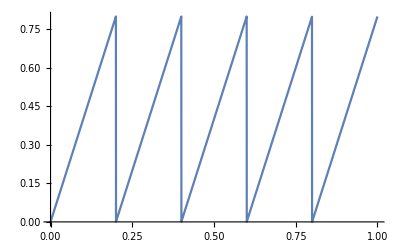

```mathematica
Plot[fn2[h],{h,0,1}]
```

```mathematica
fn2[0.24]
```

0.16

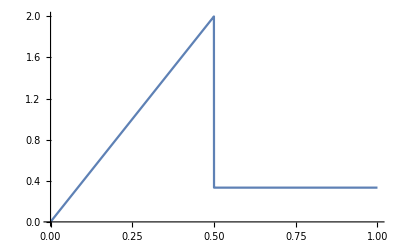

```mathematica
Plot[fn2[x],{x,0,1}]
```

Problem is only solved when both the function and variable is local, so that there is no confusion of variable names being passed.

```mathematica
Plot[fn3[x],{x,0,1}]
```

-Graphics-

#### When doing testing, always use SameQ to test symbols

Otherwise it may not evaluate

```mathematica
TemporalData==TemporalData
```

True

```mathematica
Dataset==TemporalData
```

Dataset==TemporalData

```mathematica
Dataset===TemporalData
```

False

#### TimeSeries

```mathematica
TimeSeries[{{1,1},{2,2},{3,3}}]["ValueDimensions"]
```

1

```mathematica
TimeSeries[{{1,{1,2}},{2,{2,2}},{3,{3,3}}}]["ValueDimensions"]
```

2

```mathematica
TimeSeries[{{1,{1}},{2,{2}},{3,{3}}}]["ValueDimensions"]
```

{1}

### When a variable is updated in a dynamic content, it cannot be statically set

```mathematica
Manipulate[t=Max[n,3];t,{n,1,10}]
```

```mathematica
t=100;
```

```mathematica
t
```

5.47

## Others

#### DateObject may appear the same, but in fact not

This will cause problem when comparing them during logical operations, especially with function that compares dates using SameQ. 
DateObject can be different depending on their constituent indices being integer or real number.

```mathematica
t1=DateObject[{2013,12,5,1,0,0.},"Instant","Gregorian",8.];
```

```mathematica
DateList[t1]
```

{2013,12,5,1,0,0.}

```mathematica
t2=DateObject[{2013,12,5,1,0,0}]
```

Thu 5 Dec 2013 01:00:00GMT+8.

```mathematica
t1==t2
```

True

```mathematica
t1===t2
```

False

```mathematica
JoinAcross[{<|"t"->t1,"a"->1|>},{<|"t"->t2,"b"->2|>},"t","Outer"]
```

{<|t→Thu 5 Dec 2013 01:00:00GMT+8.,a→Missing[Unmatched],b→2|>,<|t→Thu 5 Dec 2013 01:00:00GMT+8.,a→1,b→Missing[Unmatched]|>}

## On certain functions

#### On FindRoot

it returns a replacement rule. The already existing values assigned ot the variable name doesn’t matter. Don’t need to define it as local variable in a Module.

```mathematica
t=2;
localF=FindRoot[#+t==0,{t,-1}]&;
{t+2,V=t/.(localF@1),t}
(* V is not affected by the value of t *)
```

{4,-1.,2}

#### On NIntegrate

Sometimes the convergence may be a problem for highly oscillatory curves. In such cases, adjust the method and MaxRecursion to solve the problem.

```mathematica
NIntegrate[Interpolation[spectrum,InterpolationOrder->1][x],{x,First[wavelength],Last[wavelength]},Method->"Trapezoidal",MaxRecursion->20]
```

#### On day and time and geolocation functionalities

Sometimes system timezone and location may be set to other than where the machine is! 
Make sure to specify $TimeZone and $GeoLocation, or specify in corresponding options in functions (such as DateObject, DaylightQ) when running unsupervised calculations.

#### ReplaceAll

Cannot use short form to replace numbers because . will be interpreted as decimal point.

```mathematica
data/.0->1
```

#### JoinAcross

When joining associations with repeated values associated with the same key, all combinations are listed in the result, irrespective of joining method.

```mathematica
JoinAcross[
{<|a->1,b->X|>,<|a->2,b->Y|>,<|a->1,b->Z|>},
{<|a->1,d->X|>,<|a->2,d->Y|>,<|a->1,d->DD|>},
Key[a]]
```

{<|a→1,b→X,d→X|>,<|a→1,b→Z,d→X|>,<|a→2,b→Y,d→Y|>,<|a→1,b→X,d→DD|>,<|a→1,b→Z,d→DD|>}

```mathematica
JoinAcross[
{<|time->1|>,<|time->2|>,<|time->1|>},
{<|time->1,d->X|>,<|time->2,d->Y|>},
Key[time]]
```

{<|time→1,d→X|>,<|time→1,d→X|>,<|time→2,d→Y|>}

```mathematica
JoinAcross[
{<|time->1|>,<|time->2|>},
{<|time->1,d->X|>,<|time->2,d->Y|>,<|time->1,d->Z|>},
Key[time],"Left"]
```

{<|time→1,d→X|>,<|time→2,d→Y|>,<|time→1,d→Z|>}

#### ListDensityPlot3D

Input array for ListDensityPlot3D is awkwardly in format {z,y,x} corresponding to array of dimension {r,s,t}, i.e. dimension r should correspond to variable z. When specifying DataRange, AxesLabel, or PlotRange, the order is then conventionally {x,y,z}, so range should be specified in the order of {t,s,r}, not as suggested in help manual which is {r,s,t}!

```mathematica
data=Table[Exp[-(x^2+y^2+z^2)],{z,-1,1,1/5},{y,-1,1,1/10},{x,-1,1,1/20}];
data//Dimensions
```

{11,21,41}

```mathematica
ListDensityPlot3D[data,DataRange->Automatic,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(* this is equivalent to: *)
ListDensityPlot3D[data,DataRange->{{1,41},{1,21},{1,11}},AxesLabel->{x,y,z}] (* DataRange not {{1,11},{1,21},{1,41}} as one might think! *)
```

```mathematica
ListDensityPlot3D[data,DataRange->{{-4,4},{-2,2},{-1,1}},AxesLabel->{x,y,z},PlotRange->{{-1,3},All,All}]
```

-Graphics3D-

### On Datasets

## On plotting

place legends inside a chart

Note the syntax of Placed, two pairs of coordinates should be given instead of one:
{{position in the graphics}, {part of the legend located in the position of the graphics}}
The second option can be omitted if not necessary.

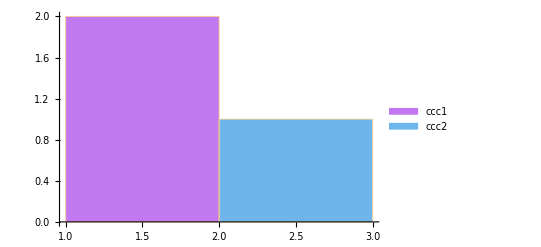

```mathematica
Histogram[{1,1,2},ChartLegends->Placed[{"ccc1","ccc2"},{{0.8,0.8}}],ChartStyle->"Pastel"]
```

Unable to change plot style in Show

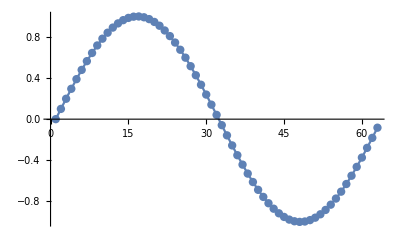

```mathematica
Show[ListLinePlot[Table[Sin[x],{x,0,2 Pi,0.1}],Mesh->All],PlotStyle->Red]
```

it still gives a plot in blue instead of red. 
Show allows only option that can be applied to graphics to be given. PlotStyle and ChartLabels are not generic Graphics objects, and options only for specific subsets of Graphics functionality (Plots and charts in this case). As such these two options are will not take effect inside of Show.